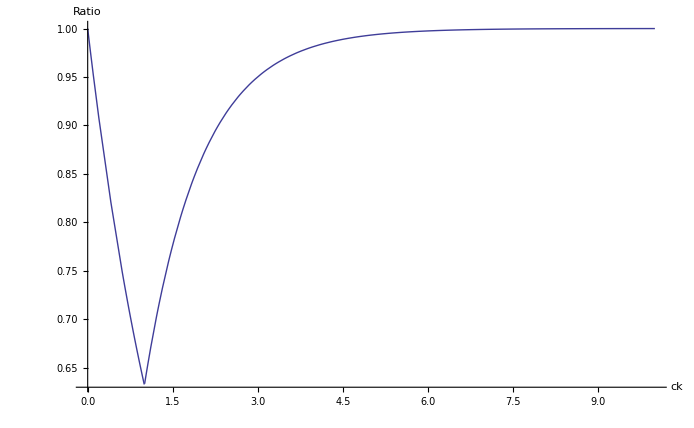

```mathematica
Plot[(1-Exp[-ck])/Min[ck,1],{ck,0,10}, AxesLabel->{Style[ck,16],Style[Ratio,16],{Style["t",Italic,Large]}}, PerformanceGoal->"Quality", AxesStyle->Directive[Black, 16]]
```

```mathematica
a=5;Reduce[1-Exp[-ck]*(ck^a-1)/(ck-1)>.95,ck, WorkingPrecision->50]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ck>13.4767

```mathematica
a=3;1-Exp[-ck]*(ck^a-1)/(ck-1)==.95/.ck->10
```

False